```mathematica
ClearAll["Global`*"]
ClearAll[n,m]
$Assumptions={0<b1<b2<1,0<d1<d2<1,0<αm<1,0<αn<1,ω∈Reals,k∈Reals};

ra=3/2;
ri=ra/3;
b1=0.278;
b2=0.365;
d1=0.267;
d2=0.445;
αn=0.028;
αm=0.147;

σ1[x_,a_,α_]:=1/(1+Exp[-(x-a)4/α])
σ2[x_,a_,b_,α_]:=σ1[x,a,α](1-σ1[x,b,α])
σm[x_,y_,m_,α_]:=x(1-σ1[m,0.5,α])+y σ1[m,0.5,α]
s[n_,m_]:=σ2[n,σm[b1,d1,m,αm],σm[b2,d2,m,αm],αn]*2-1

M=π ri^2;
NN=π(ra^2-ri^2);
m[f_]:=Integrate[f[r]*2π r/M,{r,0,ri}]
n[f_]:=Integrate[f[r]*2π r/NN,{r,ri,ra}]
S[f_]:=s[n[f],m[f]]
sGrad = Grad[s[n1,m1],{n1,m1}];

sLin[n0_,m0_][n_,m_]:=(sGrad/.{n1->n0,m1->m0}).({n,m}-{n0,m0})+s[n0,m0]
Slin[f0_][f_]:=sLin[n[f0],m[f0]][n[f],m[f]]
```

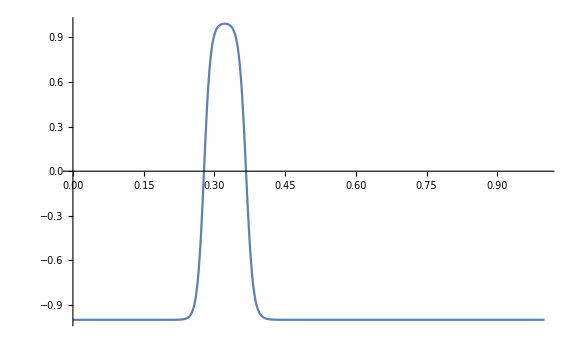

```mathematica
SkConst=S[k&];
Plot[SkConst,{k,0,1},PlotRange->All]
{V1,V2}=k/.NSolve[{SkConst==0,0<k<1},k];
```

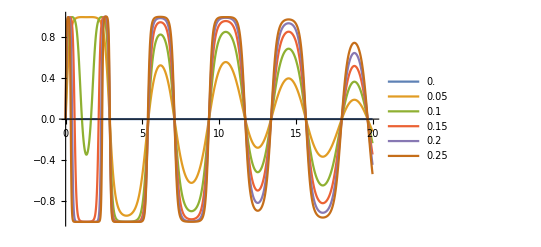

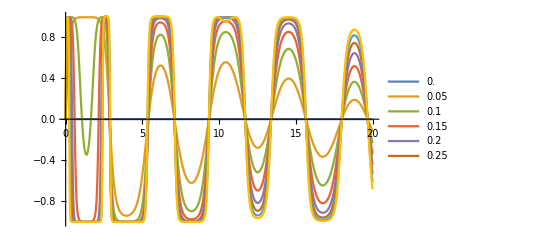

```mathematica
SkSin=Table[S[V1+ A Sin[k#]&],{A,0,V1,0.05}];
Plot[SkSin,{k,0,20},PlotRange->All,PlotLegends->Table[A,{A,0,V1,0.05}]]
SkSin=Table[S[V1+ A Sin[k#]&],{A,0,V2,0.05}];
Plot[SkSin,{k,0,20},PlotRange->All,PlotLegends->Table[A,{A,0,V1,0.05}]]
```

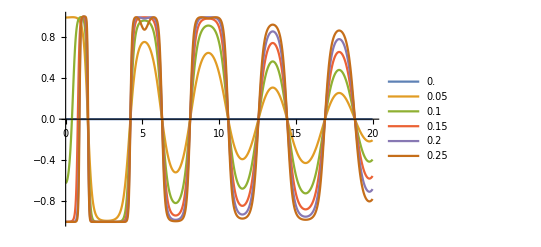

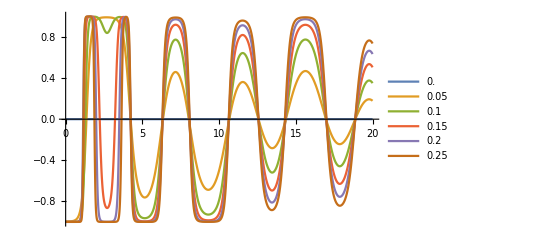

```mathematica
SkSin=Table[S[V1+ A Cos[k#]&],{A,0,V1,0.05}];
Plot[SkSin,{k,0,20},PlotRange->All,PlotLegends->Table[A,{A,0,V1,0.05}]]
SkSin=Table[S[V2+ A Cos[k#]&],{A,0,V1,0.05}];
Plot[SkSin,{k,0,20},PlotRange->All,PlotLegends->Table[A,{A,0,V1,0.05}]]
```